# Try 15

```mathematica
SetOptions[SelectedNotebook[],Background->LightGreen]
```

## Set Up

In the Set Up Section, we
- import the relevant xAct packages
- define the functions G_n
- Make functions for the background equations
- define all the w_n coefficients and stability coefficients q_x, F_x

```mathematica
Block[{Print},<<xAct`xTensor`]
Block[{Print},<<xAct`xTras`]
SetOptions[AutomaticRules,Verbose->False];
$DefInfoQ = False;
$PrePrint=ScreenDollarIndices;
```

```mathematica
DefScalarFunction/@{A0,G2,G2x,dG2x,ddG2x,G3,G3x,dG3x,dG3xx,G4,G5,g5,G6}
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
DefScalarFunction/@{aa,H}
```

{Null,Null}

Scale factor a(t):

```mathematica
aa'[t_]:=H[t]aa[t]
aa''[t_]:=D[H[t]aa[t],t]
```

Background equations ρM and pM

```mathematica
ρM[t_] := -(- G2[XX]-6 G4[XX] H[t]^2+6  H[t]^2 A0[t]^2 G4'[XX]+2 H[t]^3 A0[t]^3 G5'[XX])
```

```mathematica
pM[t_] := -(G2[XX]+6 G4[XX] H[t]^2-6  H[t]^2 A0[t]^2 G4'[XX]-2 H[t]^3 A0[t]^3 G5'[XX]+4 G4[XX] H'[t]-4  A0[t]^2 G4'[XX] H'[t]-2 H[t] A0[t]^3 G5'[XX] H'[t]+ A0[t]^2 G3'[XX] A0'[t]-4 H[t] A0[t] G4'[XX] A0'[t]-3 H[t]^2 A0[t]^2 G5'[XX] A0'[t]-4 H[t] A0[t]^3 A0'[t] G4''[XX]- H[t]^2 A0[t]^4 A0'[t] G5''[XX])
```

Equations of Motion for A_0

```mathematica
EoM[t_] := G2'[XX]+H[t](6 H[t] G4'[XX]-3 A0[t] (G3'[XX]-H[t]^2 G5'[XX])+6 A0[t]^2 H[t] G4''[XX]+A0[t]^3 H[t]^2 G5''[XX])
```

```mathematica
XX = A0[t]^2/2
```

A0[t]^2/2

Tensor Stability Coefficients

```mathematica
qt[t_]:=2 G4[XX]- 2 A0[t]^2 D[G4[x],x]-H[t]A0[t]^3 D[G5[x],x]/.{x-> XX}
```

```mathematica
Ft[t_]:= 2 G4[x]-Derivative[1][A0][t]A0[t]^2 D[G5[x],x]/.{x->XX}
```

Vector Stability Coefficients

```mathematica
qv[t_]:= G2F[x]+ 2 A0[t]^2 G2Y[x]+4H[t]A0[x]g5[x]+2H[t]^2(G6[x]+D[G6[x],x]A0[t]^2)/.{x-> XX}
```

```mathematica
α1[t_]:=G2F[x]+2 A0'[t]g5[x]+2(H[t]^2+H'[t])G6[x]+ 2 A0[t]g5[x]+ 2 A0[t]A0'[t]Derivative[1][G6][x]/.{x-> XX}
```

```mathematica
w1[t_]:=  -H[t]^2(A0[t]^3(G5'[XX]+A0[t]^2 Derivative[2][G5][XX]))-2 H[t](2 (G4[XX]+A0[t]^4 Derivative[2][G4][XX]))+A0[t]^3 Derivative[1][G3][XX]
```

```mathematica
w2[t_] := w1[t] + 2 H[t]qt[t]
```

```mathematica
D[EoM[t],t]//Simplify//Expand
```

-3 H[t] A0'[t] G3'[A0[t]^2/2]+3 H[t]^3 A0'[t] G5'[A0[t]^2/2]-3 A0[t] G3'[A0[t]^2/2] H'[t]+12 H[t] G4'[A0[t]^2/2] H'[t]+9 A0[t] H[t]^2 G5'[A0[t]^2/2] H'[t]+A0[t] A0'[t] G2''[A0[t]^2/2]-3 A0[t]^2 H[t] A0'[t] G3''[A0[t]^2/2]+18 A0[t] H[t]^2 A0'[t] G4''[A0[t]^2/2]+12 A0[t]^2 H[t] H'[t] G4''[A0[t]^2/2]+6 A0[t]^2 H[t]^3 A0'[t] G5''[A0[t]^2/2]+3 A0[t]^3 H[t]^2 H'[t] G5''[A0[t]^2/2]+6 A0[t]^3 H[t]^2 A0'[t] G4^(3)[A0[t]^2/2]+A0[t]^4 H[t]^3 A0'[t] G5^(3)[A0[t]^2/2]

```mathematica
D[EoM[t],t]/.{ H'[t]-> 0}//Simplify//Expand
```

-3 H[t] A0'[t] G3'[A0[t]^2/2]+3 H[t]^3 A0'[t] G5'[A0[t]^2/2]+A0[t] A0'[t] G2''[A0[t]^2/2]-3 A0[t]^2 H[t] A0'[t] G3''[A0[t]^2/2]+18 A0[t] H[t]^2 A0'[t] G4''[A0[t]^2/2]+6 A0[t]^2 H[t]^3 A0'[t] G5''[A0[t]^2/2]+6 A0[t]^3 H[t]^2 A0'[t] G4^(3)[A0[t]^2/2]+A0[t]^4 H[t]^3 A0'[t] G5^(3)[A0[t]^2/2]

```mathematica
w2[t]/.{ H'[t]-> 0}//Simplify//Expand
```

A0[t]^3 G3'[A0[t]^2/2]-4 A0[t]^2 H[t] G4'[A0[t]^2/2]-3 A0[t]^3 H[t]^2 G5'[A0[t]^2/2]-4 A0[t]^4 H[t] G4''[A0[t]^2/2]-A0[t]^5 H[t]^2 G5''[A0[t]^2/2]

```mathematica
w3[t_]:= - 2 A0[t]^2 qv[t]
```

```mathematica
w5[t_] := 1/2 H[t]^3 A0[t]^3(3  G5'[x]+6 A0[t]^2 G5''[x]+A0[t]^4 Derivative[3][G5][x])+3 H[t]^2 A0[t](A0[t]^3(3 G4''[x]+A0[t]^2Derivative[3][G4][x]))-3 H[t]A0[t]^3(1/2 Derivative[1][G3][x]+1/2 A0[t]^2 Derivative[2][G3][x])+1/2 A0[t]^4Derivative[2] [G2][x]/.{x-> XX}
```

```mathematica
w6[t_]:= -(w1[t] + 2 H[t]qt[t])/A0[t]-4 H[t](2 A0[t] Derivative[1][G4][x]+H[t]A0[t]^2 Derivative[1][G5][x])/.{x-> XX}//Simplify//Expand
```

```mathematica
α3[t_]:= -1/(4 H[t]A0[t])(-A0[t]w6[t] -w2[t])//Simplify//Expand
```

Vector Stability Coefficient

```mathematica
Fv[t_]:=(2 α1[x] qt[t]+ α3[t]^2)/(2 qt[t])
```

```mathematica
w4[t_]:=w5[t]-H[t]^3(3 A0[t]^3(2 Derivative[1][G5][x]+A0[t]^2 Derivative[2][G5][x]))-3 H[t]^2(2 G4[x]+ A0[t]^2(2 Derivative[1][G4][x]+ 4 A0[t]^2Derivative[2][G4][x]))+ 3 H[t](A0[t]^3Derivative[1][G3][x])/.{x-> XX}
```

```mathematica
w7[t_]:= - 2 Derivative[1][H][t](2 Derivative[1][G4][XX]+H[t]A0[t]Derivative[1][G5][x])-H[t]^2(Derivative[1][A0][t](Derivative[1][G5][x]+A0[t]^2 Derivative[2][G5][x]))- 4 H[t]A0[t]Derivative[1][A0][t]Derivative[2][G4][x]+   Derivative[1][A0][t]Derivative[1][G3][x]/.{x-> XX }
```

```mathematica
w8[t_]:= 3 H[t]w1[t]-2 w4[t]
```

```mathematica
E2[t_]:= 2 qt[t]^2/(2 H[t]qt[t]+w2[t])
```

```mathematica
E3[t_]:= -(w2[t]+A0[t]w6[t])/(4 H[t]A0[t])- qt[t]w2[t]/(A0[t](w1[t]-2 w2[t]))
```

```mathematica
αT[t_] := 1/qt[t](2 A0[t]^2 G4'[A0[t]^2/2]+A0[t]^2(H[t]A0[t]-Derivative[1][A0][t])G5'[A0[t]^2/2])
```

```mathematica
αB[t_]:= -(w1[t]-2w2[t]+ 2H[t]qt[t])/(2 H[t]qt[t])
```

```mathematica
αK[t_]:= 6 + 12 αB[t]+2(w4[t]+4w5[t]+ 2 w8[t])/(H[t]^2 qt[t])
```

Scalar Stability Coefficients

```mathematica
qs[t_]:=qt[t](3 w2[t]^2 + 4 w5[t]qt[t])/(2 H[t]qt[t]+w2[t])^2
```

```mathematica
Fs[t_]:=-Ft[t]+ 2 E3[t]^2/qv[t]-2 qt[t]^2(ρM[t]+pM[t])/(w1[t]-2 w2[t])^2 + 1/aa[t]D[aa[t]E2[t],t]//Simplify
```

```mathematica
-(2 qt[t] H'[t]+ w2[t]/A0[t] A0'[t])/.{H[t]-> 0}
```

-A0[t]^2 A0'[t] G3'[A0[t]^2/2]-2 (2 G4[A0[t]^2/2]-2 A0[t]^2 G4'[A0[t]^2/2]) H'[t]

```mathematica
ρM[t]+pM[t]/.{H[t]-> 0}
```

-A0[t]^2 A0'[t] G3'[A0[t]^2/2]-4 G4[A0[t]^2/2] H'[t]+4 A0[t]^2 G4'[A0[t]^2/2] H'[t]

```mathematica
ρM[t]+pM[t]//Simplify//Expand
```

-A0[t]^2 A0'[t] G3'[A0[t]^2/2]+4 A0[t] H[t] A0'[t] G4'[A0[t]^2/2]+3 A0[t]^2 H[t]^2 A0'[t] G5'[A0[t]^2/2]-4 G4[A0[t]^2/2] H'[t]+4 A0[t]^2 G4'[A0[t]^2/2] H'[t]+2 A0[t]^3 H[t] G5'[A0[t]^2/2] H'[t]+4 A0[t]^3 H[t] A0'[t] G4''[A0[t]^2/2]+A0[t]^4 H[t]^2 A0'[t] G5''[A0[t]^2/2]

```mathematica
3 w2[t]^2 + 4 w5[t]qt[t]//Simplify
```

A0[t]^3 (3 A0[t] (4 H[t] G4'[A0[t]^2/2]-A0[t] (G3'[A0[t]^2/2]-3 H[t]^2 G5'[A0[t]^2/2])+4 A0[t]^2 H[t] G4''[A0[t]^2/2]+A0[t]^3 H[t]^2 G5''[A0[t]^2/2])^2+2 (2 G4[A0[t]^2/2]-A0[t]^2 (2 G4'[A0[t]^2/2]+A0[t] H[t] G5'[A0[t]^2/2])) (A0[t] G2''[A0[t]^2/2]-3 H[t] (G3'[A0[t]^2/2]+A0[t]^2 G3''[A0[t]^2/2])+6 H[t]^2 (3 A0[t] G4''[A0[t]^2/2]+A0[t]^3 G4^(3)[A0[t]^2/2])+H[t]^3 (3 G5'[A0[t]^2/2]+6 A0[t]^2 G5''[A0[t]^2/2]+A0[t]^4 G5^(3)[A0[t]^2/2])))

```mathematica
qt[t]
```

2 G4[A0[t]^2/2]-2 A0[t]^2 G4'[A0[t]^2/2]-A0[t]^3 H[t] G5'[A0[t]^2/2]

```mathematica
ρM[t]+pM[t]/.{H[t]-> 0}
```

-A0[t]^2 A0'[t] G3'[A0[t]^2/2]-4 G4[A0[t]^2/2] H'[t]+4 A0[t]^2 G4'[A0[t]^2/2] H'[t]

```mathematica
D[EoM[t],t]/.{H[t]-> 0}
```

-3 A0[t] G3'[A0[t]^2/2] H'[t]+A0[t] A0'[t] G2''[A0[t]^2/2]

```mathematica
3 w2[t]^2 + 4 w5[t]qt[t]/.{H[t]->0}
```

3 A0[t]^6 G3'[A0[t]^2/2]^2+2 A0[t]^4 (2 G4[A0[t]^2/2]-2 A0[t]^2 G4'[A0[t]^2/2]) G2''[A0[t]^2/2]

```mathematica
EoM[t]//Expand
```

G2'[A0[t]^2/2]-3 A0[t] H[t] G3'[A0[t]^2/2]+6 H[t]^2 G4'[A0[t]^2/2]+3 A0[t] H[t]^3 G5'[A0[t]^2/2]+6 A0[t]^2 H[t]^2 G4''[A0[t]^2/2]+A0[t]^3 H[t]^3 G5''[A0[t]^2/2]

```mathematica
Fs[t]/.{H[t]-> 0}//Simplify
```

-2 G4[A0[t]^2/2]+(8 G4[A0[t]^2/2]^2)/(A0[t]^2 (G2F[A0[t]^2/2]+2 A0[t]^2 G2Y[A0[t]^2/2]))+A0[t]^2 A0'[t] G5'[A0[t]^2/2]+(8 (G4[A0[t]^2/2]-A0[t]^2 G4'[A0[t]^2/2])^2 (4 G4[A0[t]^2/2] H'[t]+A0[t]^2 (A0'[t] G3'[A0[t]^2/2]-4 G4'[A0[t]^2/2] H'[t])))/(A0[t]^6 G3'[A0[t]^2/2]^2)-(8 (G4[A0[t]^2/2]-A0[t]^2 G4'[A0[t]^2/2]) (A0[t]^2 G5'[A0[t]^2/2] H'[t]+2 A0'[t] (G4'[A0[t]^2/2]+A0[t]^2 G4''[A0[t]^2/2])))/(A0[t]^2 G3'[A0[t]^2/2])-1/(A0[t]^6 G3'[A0[t]^2/2]^2)8 (G4[A0[t]^2/2]-A0[t]^2 G4'[A0[t]^2/2])^2 (4 G4[A0[t]^2/2] H'[t]+A0[t]^2 (3 A0'[t] G3'[A0[t]^2/2]-8 G4'[A0[t]^2/2] H'[t])+A0[t]^4 (A0'[t] G3''[A0[t]^2/2]-4 H'[t] G4''[A0[t]^2/2]))

```mathematica
qs[t]/.{H[t]-> 0}
```

((2 G4[A0[t]^2/2]-2 A0[t]^2 G4'[A0[t]^2/2]) (3 A0[t]^6 G3'[A0[t]^2/2]^2+2 A0[t]^4 (2 G4[A0[t]^2/2]-2 A0[t]^2 G4'[A0[t]^2/2]) G2''[A0[t]^2/2]))/(A0[t]^6 G3'[A0[t]^2/2]^2)

## Functions

In this Section we give specific examples for G_n and define the background H(t)

```mathematica
HH[t_]:= H0 ArcTan[α t]
```

```mathematica
dHH[t_]:= (H0 α)/(1+t^2 α^2)
```

```mathematica
G2[x_]:= c20 + c21 x + c22 x^2
G2Y[x_]:= 0
G2F[x_]:= c
G3[x_]:= c30 + c31 x
G4[x_]:= c40 + c41 x + c42 x^2
G5[x_]:= c50+c51 x
```

```mathematica
G4[x_]:= Mpl^2/2
G5[x_]:= 0
```

Equation of Motion for this example

```mathematica
EoM[t]
```

c21+c22 A0[t]^2-3 c31 A0[t] H[t]

Two solutions for A0:

```mathematica
Solve[EoM[t]==0, A0[t]]
```

{{A0[t]→(3 c31 H[t]-√(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22)},{A0[t]→(3 c31 H[t]+√(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22)}}

```mathematica
RuleH = {H[t]-> HH[t], H'[t]-> dHH[t]}
```

{H[t]→H0 ArcTan[t α],H'[t]→(H0 α)/(1+t^2 α^2)}

```mathematica
D[A0[t],t]
```

A0'[t]

```mathematica
D[(3 c31 H[t]+ϵ √(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22),t]//Simplify
```

(3 c31 (1+(3 c31 ϵ H[t])/(√(-4 c21 c22+9 c31^2 H[t]^2))) H'[t])/(2 c22)

Define Rule for A0. ϵ denotes the sign plus/,minus

```mathematica
RuleA0 = {A0[t]->(3 c31 H[t]+ϵ √(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22), A0'[t]->(3 c31 (1+(3 c31 ϵ H[t])/(√(-4 c21 c22+9 c31^2 H[t]^2))) H'[t])/(2 c22)};
```

```mathematica
Bounce = {H[t]-> 0, H'[t]-> H0 α, t-> 0}
```

{H[t]→0,H'[t]→H0 α,t→0}

Solution at the Bounce

```mathematica
A0[t]/.RuleA0/.Bounce
```

(√(-c21 c22) ϵ)/c22

```mathematica
Rulex = {x-> A0[t]^2/2}
```

{x→A0[t]^2/2}

```mathematica
RulePlus = {ϵ-> 1}
RuleMinus = {ϵ-> -1}
```

{ϵ→1}

{ϵ→-1}

Conditions for G2 at the Bounce:

```mathematica
G2[x]/.Rulex/.RuleA0/.Bounce
```

c20-(c21^2 ϵ^2)/(2 c22)+(c21^2 ϵ^4)/(4 c22)

```mathematica
G2[x]/.Rulex/.RuleA0/.Bounce/.RulePlus
```

c20-c21^2/(4 c22)

```mathematica
D[G2[x],x]/.Rulex/.RuleA0/.Bounce
```

c21-c21 ϵ^2

```mathematica
D[D[G2[x],x],x]/.Rulex/.RuleA0/.Bounce
```

2 c22

## Stability

Stability Conditions:

A0 at the Bounce

```mathematica
A0[t]/.RuleA0/.Bounce
```

(√(-c21 c22) ϵ)/c22

Specify the Functions

```mathematica
G5[x_]:= 0
g5[x_]:= 0
G6[x_]:= 0
```

```mathematica
G4[x_]:= Mpl^2/2
```

ρM + pM at the Bounce

```mathematica
ρM[t]+pM[t]/.RuleA0/.Bounce/.RulePlus//Simplify
```

(3 c21 c31^2 H0 α)/(2 c22^2)-2 H0 Mpl^2 α

ρM at the Bounce

```mathematica
ρM[t]/.RuleA0/.Bounce/.RulePlus//Simplify
```

c20-c21^2/(4 c22)

We now analyze the stbility coefficients at the Bounce and at infinity

### qT

qT is constant

```mathematica
qt[t]//Simplify
```

Mpl^2

### qV

qV is constant

```mathematica
qv[t]/.RuleA0/.Bounce
```

c

### qS

qS at the bounce

```mathematica
qs[t]/.RuleA0/.Bounce/.RulePlus//Simplify
```

3 Mpl^2-(4 c22^2 Mpl^4)/(c21 c31^2)

Only this is necesary to have qS > 0

```mathematica
(3 w2[t]^2 + 4 w5[t]qt[t])/.RuleA0/.Bounce/.RulePlus//Simplify
```

(c21^2 (-3 c21 c31^2+4 c22^2 Mpl^2))/c22^3

qS at infinity

```mathematica
Simplify[Limit[qs[t]/.RuleA0/.RuleH/.RulePlus, t-> ∞], α> 0]
```

(64 Mpl^2 (c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^6))/(c22^6 (64 H0 Mpl^2 π+(c31 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^3)/c22^3)^2)

```mathematica
Simplify[Limit[(3 w2[t]^2 + 4 w5[t]qt[t])/.RuleA0/.RuleH, t-> ∞], α>0]
```

1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)

Setting ϵ

```mathematica
1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)/.RulePlus//Simplify
```

1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^6)

```mathematica
1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)/.RuleMinus//Simplify
```

1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^6)

Or make this simpler conditon at infinity ... they are still not very useful

```mathematica
Simplify[Limit[(3 w2[t]^2 + 4 w5[t]qt[t])/.RuleA0/.RuleH, t-> -∞], α>0]
```

1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)

```mathematica
1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)/.RulePlus
```

1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2))^6)

```mathematica
1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)/.RuleMinus
```

1/(64 c22^6)(-c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (-3 c31 H0 π-√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (-3 c31 H0 π-√(-16 c21 c22+9 c31^2 H0^2 π^2))^6)

```mathematica
1/(64 c22^6)(c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^3+3/64 c31^2 (-3 c31 H0 π+√(-16 c21 c22+9 c31^2 H0^2 π^2) ϵ)^6)/.RuleMinus
```

1/(64 c22^6)(-c22^3 Mpl^2 √(-16 c21 c22+9 c31^2 H0^2 π^2) (-3 c31 H0 π-√(-16 c21 c22+9 c31^2 H0^2 π^2))^3+3/64 c31^2 (-3 c31 H0 π-√(-16 c21 c22+9 c31^2 H0^2 π^2))^6)

We just make sure, that qs[t] does not cross zero. So wie solve qs[t]= 0 and ensure that these solutions don’t exist.
We solve for u = arctan( α t) the solution does not exist if |u| > π/2

```mathematica
Solve[qs[t]==0/.RuleA0/.RuleH/.RulePlus/.{ArcTan[t α]-> u}, u]
```

{{u→-(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)-(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)-(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→-(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)+(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)+(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)}}

```mathematica
Solve[qs[t]==0/.RuleA0/.RuleH/.RuleMinus/.{ArcTan[t α]-> u}, u]
```

{{u→-(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)-(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)-(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→-(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)+(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)},{u→(√((15 c21 c22)/(c31^2 H0^2)-(2 c22^3 Mpl^2)/(c31^4 H0^2)+(√(c31^4 H0^4 Mpl^2 (6 c21 c31^2+c22^2 Mpl^2) (3 c21 c31^2+2 c22^2 Mpl^2)^2))/(c31^6 H0^4 Mpl^2)))/(3 √6)}}

### Fs

We repeat the same analysis for the stability coefficient FS

First at the bounce:

```mathematica
Fs[t]/.RuleA0/.Bounce/.RulePlus//Simplify
```

-Mpl^2-(2 c22 Mpl^4 (c21+3 c H0 α))/(c c21^2)

Again ensure that Fs does not cross 0:

```mathematica
Fs[t]/.RuleA0/.RuleH/.{ArcTan[t α]-> u}
```

-((c31 Mpl^2 (3 c31 H0 u+√(-4 c21 c22+9 c31^2 H0^2 u^2) ϵ)^2 ((6 c c31 H0 Mpl^2 α (1+(3 c31 H0 u ϵ)/(√(-4 c21 c22+9 c31^2 H0^2 u^2))))/(c22 (1+t^2 α^2))+(c H0 Mpl^2 u (3 c31 H0 u+√(-4 c21 c22+9 c31^2 H0^2 u^2) ϵ))/c22-(c31 Mpl^2 (3 c31 H0 u+√(-4 c21 c22+9 c31^2 H0^2 u^2) ϵ)^2)/(2 c22^2)+(c c31 (3 c31 H0 u+√(-4 c21 c22+9 c31^2 H0^2 u^2) ϵ)^4)/(16 c22^4)))/(4 c c22^2 (2 H0 Mpl^2 u+(c31 (3 c31 H0 u+√(-4 c21 c22+9 c31^2 H0^2 u^2) ϵ)^3)/(8 c22^3))^2))

Now set H =  5.5*10^(-6) and α = 1/200

```mathematica
RuleExample = {H0-> 5.5*10^(-6),α-> 1/200, Mpl-> 1}
```

{H0→5.5×10^-6,α→1/200,Mpl→1}

```mathematica
qs[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample
```

((3 c31^2 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^6)/(64 c22^6)+4 (-(1.03125×10^-6 c31 ArcTan[t/200] (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/c22^3+((0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(16 c22^3)))/(0.000011 ArcTan[t/200]+(c31 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/(8 c22^3))^2

The following plot can be manipulated to see, what set of coefficients gives us a positive solution. A possibility is c21 = -2, c22 = 1, c31 = -1

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c21,-10,10},{c22,-10,10},{c31,-10,10}]
```

```mathematica
qs[t]/.RuleA0/.RuleH/.RuleMinus/.RuleExample
```

((3 c31^2 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^6)/(64 c22^6)+4 (-(1.03125×10^-6 c31 ArcTan[t/200] (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/c22^3+((0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(16 c22^3)))/(0.000011 ArcTan[t/200]+(c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/(8 c22^3))^2

The same for the Minus case

```mathematica
Manipulate[Plot[((3 c31^2 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7224999999999996*^-10 c31^2 ArcTan[t/200]^2))^6)/(64 c22^6)+4 (-1/c22^3 1.03125*^-6 c31 ArcTan[t/200] (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7224999999999996*^-10 c31^2 ArcTan[t/200]^2))^3+((0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7224999999999996*^-10 c31^2 ArcTan[t/200]^2))^4)/(16 c22^3)))/(0.000011 ArcTan[t/200]+(c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7224999999999996*^-10 c31^2 ArcTan[t/200]^2))^3)/(8 c22^3))^2,{t,-2000,2000}],{c21,-10,10},{c22,-10,10},{c31,-10,10}]
```

Do the same for Fs

```mathematica
Fs[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample
```

-((c31 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2 ((1.65×10^-7 c c31 (1+(0.0000165 c31 ArcTan[t/200])/(√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))))/(c22 (1+t^2/40000))+(5.5×10^-6 c ArcTan[t/200] (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2)))/c22-(c31 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2)/(2 c22^2)+(c c31 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(16 c22^4)))/(4 c c22^2 (0.000011 ArcTan[t/200]+(c31 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/(8 c22^3))^2))

The coefficients can be adjusted. Possible values: c= 1, c21 = 1, c22 = -1, c31 = 5

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10}]
```

The same for the negative case

```mathematica
Fs[t]/.RuleA0/.RuleH/.RuleMinus/.RuleExample
```

-((c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2 ((1.65×10^-7 c c31 (1-(0.0000165 c31 ArcTan[t/200])/(√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))))/(c22 (1+t^2/40000))+(5.5×10^-6 c ArcTan[t/200] (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2)))/c22-(c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2)/(2 c22^2)+(c c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(16 c22^4)))/(4 c c22^2 (0.000011 ArcTan[t/200]+(c31 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^3)/(8 c22^3))^2))

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10}]
```

Plot for ρM with coefficients. Possible values:
c = 1, c21 = 1, c22 = -1, c31 = 5, c20 = 1

```mathematica
ρM[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample
```

c20+9.075×10^-11 ArcTan[t/200]^2+(c21 (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2)/(8 c22^2)+((0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(64 c22^3)

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10},{c20,-10,10}]
```

For the Minus sign

```mathematica
ρM[t]/.RuleA0/.RuleH/.RuleMinus/.RuleExample
```

c20+9.075×10^-11 ArcTan[t/200]^2+(c21 (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2)/(8 c22^2)+((0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^4)/(64 c22^3)

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10},{c20,-10,10}]
```

Plot for ρM + pM. Possible coefficients are 
c = 1, c21 = 1, c22 = -1, c31 = 5, c20 = 1

```mathematica
ρM[t]+pM[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample
```

-(5.5×10^-8)/(1+t^2/40000)-1/(c22^3 (1+t^2/40000))1.03125×10^-8 c31^2 (1+(0.0000165 c31 ArcTan[t/200])/(√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))) (0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10},{c20,-10,10}]
```

For the Minus sign

```mathematica
ρM[t]+pM[t]/.RuleA0/.RuleH/.RuleMinus/.RuleExample
```

-(5.5×10^-8)/(1+t^2/40000)-1/(c22^3 (1+t^2/40000))1.03125×10^-8 c31^2 (1-(0.0000165 c31 ArcTan[t/200])/(√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))) (0.0000165 c31 ArcTan[t/200]-√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))^2

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10},{c20,-10,10}]
```

We can also plot A0 with 
c = 1, c21 = 1, c22 = -1, c31 = 5, c20 = 1

```mathematica
A0[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample
```

(0.0000165 c31 ArcTan[t/200]+√(-4 c21 c22+2.7225×10^-10 c31^2 ArcTan[t/200]^2))/(2 c22)

```mathematica
Manipulate[Plot[%,{t,-2000,2000}],{c,-10,10},{c21,-10,10},{c22,-10,10},{c31,-10,10},{c20,-10,10}]
```

```mathematica
A0[t]/.RuleA0
```

(3 c31 H[t]+ϵ √(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22)

```mathematica
D[A0[t],t]/.RuleA0
```

(3 c31 (1+(3 c31 ϵ H[t])/(√(-4 c21 c22+9 c31^2 H[t]^2))) H'[t])/(2 c22)

```mathematica
H[t]/.RuleH
```

H0 ArcTan[t α]

```mathematica
D[H[t],t]/.RuleH
```

(H0 α)/(1+t^2 α^2)

## Example

We now look at a specific example

We show that all coefficients remain stable

```mathematica
RuleExample = {H0->5.5*^-6,α->1/200,Mpl->1, c20-> 0, c21-> 0.75, c22-> -1, c31-> 2, c-> 1}
```

{H0→5.5×10^-6,α→1/200,Mpl→1,c20→0,c21→0.75,c22→-1,c31→2,c→1}

```mathematica
RuleArcTan = {ArcTan[t α]-> u}
```

{ArcTan[t α]→u}

Find conditions on the coefficients for stability

### Stability

```mathematica
π/2
```

π/2

We always need - π/2 < u < π/2, so that ArcTan[αt] = u has a solution

```mathematica
qv[t]
```

c

```mathematica
Fv[t]
```

c

#### ρM

```mathematica
ρM[t]/.RuleA0/.Bounce/.RuleExample/.RulePlus
```

0.140625

```mathematica
ρM[t]/.RuleA0/.Bounce/.RuleExample/.RuleMinus
```

0.140625

```mathematica
Solve[ρM[t]==0/.RuleA0/.RuleH/.RulePlus/.RuleArcTan/.RuleExample, u]
```

{{u→-17297.4-32246.3 ⅈ},{u→-17297.4+32246.3 ⅈ},{u→20246.6}}

```mathematica
Solve[ρM[t]==0/.RuleA0/.RuleH/.RuleMinus/.RuleArcTan/.RuleExample, u]
```

{{u→-20246.6},{u→17297.4-32246.3 ⅈ},{u→17297.4+32246.3 ⅈ}}

--> No real solution for t --> ρM is always positive

#### ρM + pM

```mathematica
ρM[t]+pM[t]/.RuleA0/.Bounce/.RuleExample/.RulePlus
```

6.875×10^-8

```mathematica
Solve[ρM[t]+pM[t]==0/.RuleA0/.RuleH/.RulePlus/.RuleArcTan/.RuleExample, u]
```

{{u→-13759.1},{u→0.-58989.8 ⅈ}}

```mathematica
Solve[ρM[t]+pM[t]==0/.RuleA0/.RuleH/.RuleMinus/.RuleArcTan/.RuleExample, u]
```

{{u→0.+58989.8 ⅈ},{u→13759.1}}

No real solution for t ---> ρM + pM is always positive

#### qS

```mathematica
qs[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

1.66667

```mathematica
qs[t]/.RuleA0/.RuleH/.RulePlus/.{t-> 0}/.RuleExample
```

1.66667

```mathematica
qs[t]/.RuleA0/.Bounce/.RulePlus/.RuleExample
```

1.66667

```mathematica
qs[t]/.RuleA0/.Bounce/.RuleExample/.RulePlus
```

1.66667

```mathematica
qs[t]/.RuleA0/.Bounce/.RuleExample/.RuleMinus
```

1.66667

```mathematica
Solve[qs[t]==0/.RuleA0/.RuleH/.RulePlus/.RuleArcTan/.RuleExample, u]
```

{{u→-13759.1},{u→0.-58989.8 ⅈ}}

```mathematica
Solve[qs[t]==0/.RuleA0/.RuleH/.RuleMinus/.RuleArcTan/.RuleExample, u]
```

{{u→0.+58989.8 ⅈ},{u→13759.1}}

No real solution for t ---> qs is always positive

#### Fs

```mathematica
Fs[t]/.RuleA0/.Bounce/.RulePlus/.RuleExample
```

1.66667

```mathematica
Fs[t]/.RuleA0/.Bounce/.RuleExample/.RuleMinus
```

1.66667

Solving Fs == 0 takes very long, so we check what Fs does at infinity

```mathematica
Limit[Fs[t]/.RuleA0/.RuleH/.RulePlus, t-> ∞]/.RuleExample
```

1.66656

```mathematica
Limit[Fs[t]/.RuleA0/.RuleH/.RulePlus, t-> -∞]/.RuleExample
```

1.66677

#### cs^2

```mathematica
cs2[t_]:= Fs[t]/qs[t]
```

```mathematica
cs2[t]/.RuleA0/.RuleH/.Bounce/.RulePlus/.RuleExample
```

1.

```mathematica
NumberForm[1.000000176,16]
```

1.000000176

```mathematica
RuleExample = {H0->5.5*^-6,α->1/200,Mpl->1,c20->0,c21->0.75,c22->-1,c31->3,c->1}
```

{H0→5.5×10^-6,α→1/200,Mpl→1,c20→0,c21→0.75,c22→-1,c31→3,c→1}

```mathematica
cs2[t]/.RuleA0/.RuleH/.RulePlus/.RuleExample;
```

```mathematica
cs2[t]/.RuleA0/.RuleH/.RuleMinus/.RuleExample;
```

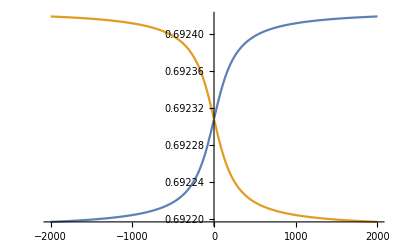

```mathematica
Plot[{% , %%}, {t,-2000,2000}]
```

```mathematica
w1[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

-1.94856

```mathematica
qt[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

1

```mathematica
w2[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

-1.94856

```mathematica
w5[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

-0.5625

```mathematica
A0[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

-0.866025

```mathematica
w4[t]-3/2H[t](w1[t]+w2[t])/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

-0.5625

```mathematica
qt[t](3 w2[t]^2 + 4 w5[t] qt[t])/(2 H[t] qt[t] + w2[t])^2/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

2.40741

```mathematica
qs[t]/.RuleA0/.RuleH/.RuleExample/.RulePlus/.{t->0}
```

2.40741

```mathematica
D[A0[t],t]/.RuleA0/.Bounce
```

(3 c31 H0 α)/(2 c22)

```mathematica
RuleA0
```

{A0[t]→(3 c31 H[t]+ϵ √(-4 c21 c22+9 c31^2 H[t]^2))/(2 c22),A0'[t]→(3 c31 (1+(3 c31 ϵ H[t])/(√(-4 c21 c22+9 c31^2 H[t]^2))) H'[t])/(2 c22)}

```mathematica
Limit[ρM[t]+pM[t]/.RuleA0/.RuleH,t-> ∞]
```

0